```mathematica
InCircle[Polygon[GeoPosition[a_]]]:=InCircle[Polygon[a/.{x_?NumericQ,y_?NumericQ}:>{y,x}]];
InCircle[Polygon[a_/;Depth[a]==4]]:=Last@(SortBy[InCircle/@a,Last]);
InCircle[a_List]:=InCircle[Polygon@a];
InCircle[Polygon[a_/;Depth[a]==3]]:=InCircle[Polygon[a]]=Module[{interior},interior=BoundaryDiscretizeGraphics@Polygon[a];
{{x,y}/.#2,Abs@#1}&@@NMinimize[SignedRegionDistance[interior,{x,y}],{x,y}∈interior]];

OutCircle[p_List]:=List@@BoundingRegion[p,"MinDisk"];
OutCircle[Polygon[GeoPosition[a_]]]:=OutCircle[Polygon[a/.{x_?NumericQ,y_?NumericQ}:>{y,x}]];
OutCircle[Polygon[a_]]:=OutCircle[Flatten[a,Depth[a]-3]];
```

```mathematica
Countries=CountryData[#,"StandardName"]&/@CountryData[];
ResultsList=Monitor[
Table[With[
{pol=CountryData[Countries[[i]],{"SchematicPolygon","Mercator"}]},
{CountryData[Countries[[i]],"Name"],
Last[InCircle[pol]]^2/Last[OutCircle[pol]]^2,
Show[Graphics[{Blue,Disk@@OutCircle[pol]}],
Graphics@pol,Graphics[{Red,Disk@@InCircle[pol]}
]]}],
{i,Length@Countries}]//SortBy[#[[2]]&]//Reverse,
Grid[{{
ProgressIndicator[i/Length@Countries],Countries[[i]]
}}]
]//TT
```

$Aborted

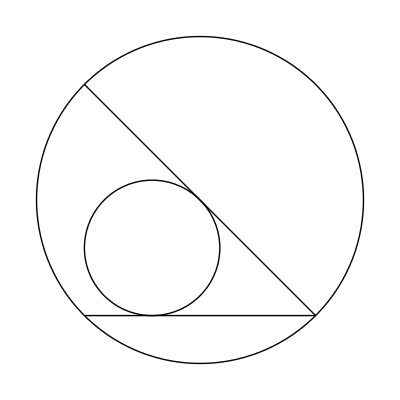

```mathematica
Graphics[{Circumsphere[#],Insphere[#],Line[#]}]&@{{0,0},{1,0},{0,1}}
```

```mathematica
LatitudeLongitude[GeoGridPosition[{1,1},"Mercator"]]
Function[{x,y},{180 Gudermannian[(π y)/180]/Pi,x}]
```

{(180 (-π/2+2 ArcTan[ⅇ^(π/180)]))/π °,1 °}

Function[{x,y},{(180 Gudermannian[(π y)/180])/π,x}]

```mathematica
RegionCentroid@DiscretizeGraphics@Polygon@Flatten[CountryData[#,{"SchematicPolygon","Mercator"}][[1]]&/@{"China","Taiwan"},1]
```

{115.766,22.217}

```mathematica
BoundingRegion[Partition[Flatten[CountryData[#,{"FullPolygon","Mercator"}][[1]]&/@{"China","Taiwan"}],2],"MinDisk"]
```

Disk[{105.128,44.2879},31.6588]

```mathematica
data=Flatten[CountryData[#,{"FullPolygon","Mercator"}][[1]]&/@{"China","Taiwan"}]
cdata=Function[{x,y},{(180 Gudermannian[(π y)/180])/π,x}]@@@Partition[data,2]
SC[{lat_,lon_}]:=r {Cos[lon °] Cos[lat °],Sin[lon °] Cos[lat °],Sin[lat °]};
r=6367.5;places=CountryData["Countries"];
geoball=Graphics3D[{Opacity[.4],Sphere[{0,0,0},r],Map[Line[Map[SC,CountryData[#,"SchematicCoordinates"],{-2}]]&,places],{Red,PointSize[Medium],Point[SC[#]]&/@cdata}},Boxed->False,SphericalRegion->True,ViewAngle->.3]
GeoPositionXYZ[#,"ITRF00"]&
ball=BoundingRegion[SC/@cdata,"MinBall"]
```

{113.551,22.7957,113.551,22.7956,113.551,22.7941,113.551,22.7939,113.554,21306,24.3125,119.672,23.9096,119.665,23.9161,119.666,23.927,119.677,23.9298}
 |  |  |  |

{{22.217,113.551},{22.2169,113.551},{22.2156,113.551},{22.2154,113.551},{22.2143,113.554},10653,{23.2444,119.672},{23.2504,119.665},{23.2604,119.666},{23.263,119.677}}
 |  |  |  |

-Graphics3D-

GeoPositionXYZ[#1,ITRF00]&

Ball[{-1184.17,4476.38,3472.28},2654.83]

```mathematica
Show[geoball,Graphics3D[{Opacity[.5],Red,ball}]]
```

-Graphics3D-

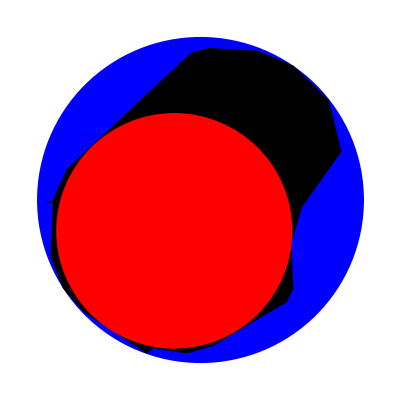
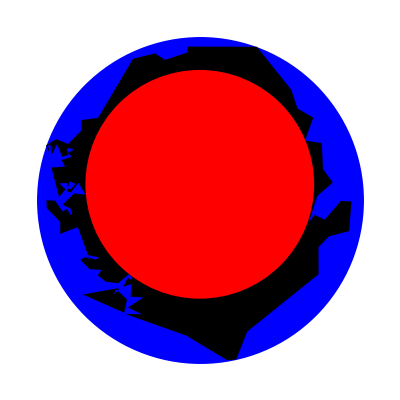
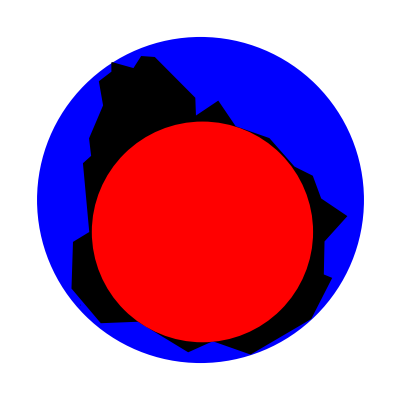
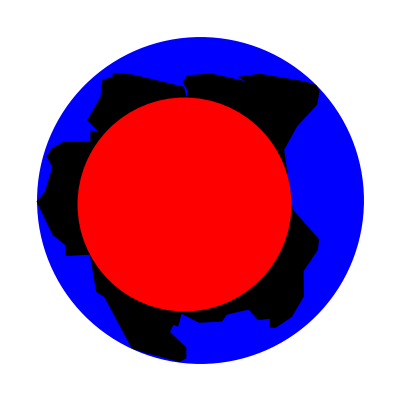
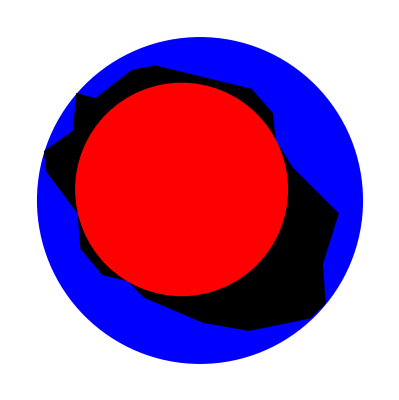
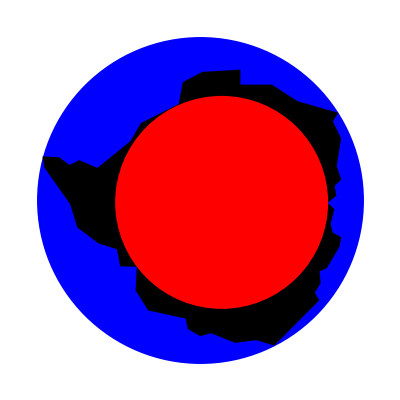
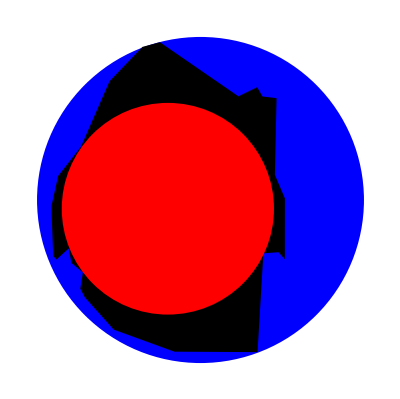
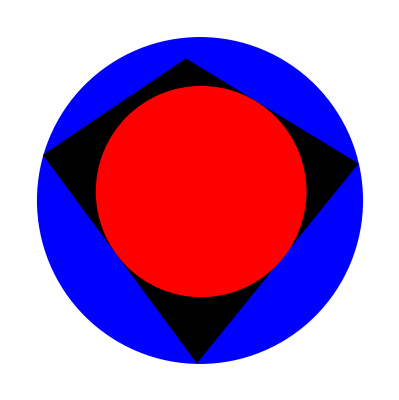
Nauru | 0.522074 | -Graphics-
Sierra Leone | 0.489491 | -Graphics-
Uruguay | 0.458073 | -Graphics-
Suriname | 0.428165 | -Graphics-
Réunion | 0.42655 | -Graphics-
Zimbabwe | 0.424476 | -Graphics-
Swaziland | 0.421394 | -Graphics-
Micronesia | 0.417626 | -Graphics-
Ivory Coast | 0.414221 | -Graphics-
Niue | 0.386979 | -Graphics-
Lesotho | 0.382229 | -Graphics-
Sudan | 0.365759 | -Graphics-
Poland | 0.365127 | -Graphics-
Macedonia | 0.364227 | -Graphics-
Algeria | 0.349713 | -Graphics-
Botswana | 0.348429 | -Graphics-
Romania | 0.344189 | -Graphics-
Kenya | 0.341899 | -Graphics-
Cambodia | 0.333243 | -Graphics-
Tanzania | 0.331697 | -Graphics-
Marshall Islands | 0.331529 | -Graphics-
Belarus | 0.327213 | -Graphics-
Andorra | 0.322265 | -Graphics-
Kosovo | 0.321314 | -Graphics-
Egypt | 0.313523 | -Graphics-
Lithuania | 0.312652 | -Graphics-
Bolivia | 0.309145 | -Graphics-
French Guiana | 0.306496 | -Graphics-
Ethiopia | 0.303705 | -Graphics-
Vatican City | 0.300494 | -Graphics-
Nigeria | 0.29947 | -Graphics-
Mauritius | 0.298072 | -Graphics-
Nicaragua | 0.277943 | -Graphics-
Pitcairn Islands | 0.2753 | -Graphics-
Saudi Arabia | 0.272941 | -Graphics-
Bosnia and Herzegovina | 0.270918 | -Graphics-
Montserrat | 0.270763 | -Graphics-
Ghana | 0.270211 | -Graphics-
Burundi | 0.263164 | -Graphics-
Niger | 0.260098 | -Graphics-
Mauritania | 0.25978 | -Graphics-
Democratic Republic of the Congo | 0.258595 | -Graphics-
Gabon | 0.251257 | -Graphics-
Barbados | 0.250081 | -Graphics-
Sri Lanka | 0.249879 | -Graphics-
South Africa | 0.245006 | -Graphics-
San Marino | 0.244711 | -Graphics-
Angola | 0.241953 | -Graphics-
Montenegro | 0.235923 | -Graphics-
Uganda | 0.235625 | -Graphics-
Spain | 0.233081 | -Graphics-
Guatemala | 0.231038 | -Graphics-
Syria | 0.229587 | -Graphics-
Chad | 0.223925 | -Graphics-
Libya | 0.22339 | -Graphics-
Brazil | 0.217471 | -Graphics-
Iceland | 0.213989 | -Graphics-
Iraq | 0.212182 | -Graphics-
Germany | 0.209603 | -Graphics-
Belgium | 0.207344 | -Graphics-
Iran | 0.207339 | -Graphics-
Luxembourg | 0.206763 | -Graphics-
Colombia | 0.20475 | -Graphics-
Bulgaria | 0.203194 | -Graphics-
Bhutan | 0.201844 | -Graphics-
France | 0.19635 | -Graphics-
Greenland | 0.196073 | -Graphics-
Burkina Faso | 0.195711 | -Graphics-
Mali | 0.192235 | -Graphics-
Venezuela | 0.191274 | -Graphics-
Senegal | 0.19051 | -Graphics-
Czech Republic | 0.189485 | -Graphics-
Rwanda | 0.18841 | -Graphics-
Zambia | 0.186266 | -Graphics-
Estonia | 0.184615 | -Graphics-
Qatar | 0.182589 | -Graphics-
Paraguay | 0.179481 | -Graphics-
Hungary | 0.177792 | -Graphics-
Kazakhstan | 0.17431 | -Graphics-
Australia | 0.173598 | -Graphics-
Namibia | 0.167747 | -Graphics-
Ukraine | 0.166802 | -Graphics-
Dominica | 0.166685 | -Graphics-
Saint Lucia | 0.166562 | -Graphics-
Switzerland | 0.16171 | -Graphics-
Dominican Republic | 0.16147 | -Graphics-
Azerbaijan | 0.160904 | -Graphics-
India | 0.159851 | -Graphics-
Kuwait | 0.159133 | -Graphics-
South Sudan | 0.157409 | -Graphics-
Afghanistan | 0.154833 | -Graphics-
South Korea | 0.151255 | -Graphics-
Ireland | 0.148027 | -Graphics-
Central African Republic | 0.148015 | -Graphics-
Austria | 0.146599 | -Graphics-
West Bank | 0.143082 | -Graphics-
Serbia | 0.138202 | -Graphics-
Mongolia | 0.137813 | -Graphics-
Cameroon | 0.13595 | -Graphics-
Latvia | 0.135629 | -Graphics-
El Salvador | 0.135448 | -Graphics-
Jersey | 0.134829 | -Graphics-
Armenia | 0.134508 | -Graphics-
Brunei | 0.132266 | -Graphics-
Turkey | 0.131118 | -Graphics-
China | 0.129926 | -Graphics-
Morocco | 0.126328 | -Graphics-
Slovakia | 0.126141 | -Graphics-
Guinea | 0.12576 | -Graphics-
Slovenia | 0.12559 | -Graphics-
Martinique | 0.12516 | -Graphics-
Taiwan | 0.124356 | -Graphics-
Benin | 0.122839 | -Graphics-
Honduras | 0.118297 | -Graphics-
Djibouti | 0.117934 | -Graphics-
Albania | 0.117554 | -Graphics-
Jordan | 0.116918 | -Graphics-
Yemen | 0.115101 | -Graphics-
Christmas Island | 0.113775 | -Graphics-
Madagascar | 0.113764 | -Graphics-
Norfolk Island | 0.112597 | -Graphics-
Liberia | 0.111723 | -Graphics-
Turkmenistan | 0.110279 | -Graphics-
Liechtenstein | 0.109398 | -Graphics-
Bangladesh | 0.10828 | -Graphics-
Oman | 0.106578 | -Graphics-
Lebanon | 0.104441 | -Graphics-
United Arab Emirates | 0.104156 | -Graphics-
Singapore | 0.102581 | -Graphics-
Moldova | 0.102479 | -Graphics-
Cyprus | 0.102051 | -Graphics-
Guyana | 0.101494 | -Graphics-
Guinea-Bissau | 0.100189 | -Graphics-
Peru | 0.0996001 | -Graphics-
Belize | 0.0990664 | -Graphics-
Finland | 0.0975627 | -Graphics-
Sint Maarten | 0.0971144 | -Graphics-
Costa Rica | 0.0943382 | -Graphics-
Haiti | 0.0939901 | -Graphics-
Isle of Man | 0.0931848 | -Graphics-
Equatorial Guinea | 0.0920211 | -Graphics-
Jamaica | 0.0909102 | -Graphics-
Eritrea | 0.0907744 | -Graphics-
Republic of the Congo | 0.0906332 | -Graphics-
Gibraltar | 0.0881212 | -Graphics-
Myanmar | 0.0854791 | -Graphics-
Tajikistan | 0.0841833 | -Graphics-
Western Sahara | 0.0814452 | -Graphics-
Georgia | 0.0807952 | -Graphics-
Canada | 0.0805524 | -Graphics-
Kyrgyzstan | 0.0801107 | -Graphics-
Tunisia | 0.0800416 | -Graphics-
Portugal | 0.0785777 | -Graphics-
North Korea | 0.0757503 | -Graphics-
Argentina | 0.074844 | -Graphics-
Thailand | 0.0746345 | -Graphics-
Nepal | 0.0737961 | -Graphics-
Malta | 0.0728392 | -Graphics-
Mayotte | 0.0724757 | -Graphics-
Laos | 0.07047 | -Graphics-
Puerto Rico | 0.0686746 | -Graphics-
Gaza Strip | 0.0680717 | -Graphics-
Guam | 0.0670868 | -Graphics-
Pakistan | 0.0668579 | -Graphics-
Papua New Guinea | 0.0666992 | -Graphics-
French Polynesia | 0.066431 | -Graphics-
Hong Kong | 0.0648756 | -Graphics-
Aruba | 0.0639821 | -Graphics-
Mozambique | 0.0630942 | -Graphics-
Guadeloupe | 0.0629544 | -Graphics-
Uzbekistan | 0.0606848 | -Graphics-
Trinidad and Tobago | 0.0587 | -Graphics-
Mexico | 0.0572333 | -Graphics-
Croatia | 0.0549513 | -Graphics-
Kiribati | 0.0538058 | -Graphics-
Fiji | 0.0531052 | -Graphics-
United States | 0.0526639 | -Graphics-
Sweden | 0.0515742 | -Graphics-
Macau | 0.0512947 | -Graphics-
Italy | 0.0496998 | -Graphics-
Ecuador | 0.0495625 | -Graphics-
Greece | 0.0486597 | -Graphics-
Samoa | 0.0482953 | -Graphics-
Saint Pierre and Miquelon | 0.0468665 | -Graphics-
Somalia | 0.0463497 | -Graphics-
Israel | 0.0452616 | -Graphics-
Denmark | 0.0448748 | -Graphics-
Saint Kitts and Nevis | 0.0438597 | -Graphics-
Togo | 0.0428668 | -Graphics-
Grenada | 0.0424669 | -Graphics-
Monaco | 0.0408272 | -Graphics-
East Timor | 0.0388008 | -Graphics-
Malawi | 0.037021 | -Graphics-
Svalbard | 0.0365756 | -Graphics-
Curacao | 0.033692 | -Graphics-
New Zealand | 0.0333436 | -Graphics-
Bahrain | 0.0324606 | -Graphics-
Vietnam | 0.0311602 | -Graphics-
United Kingdom | 0.0302831 | -Graphics-
Saint Vincent and the Grenadines | 0.0270615 | -Graphics-
Falkland Islands | 0.0255062 | -Graphics-
Antigua and Barbuda | 0.0251459 | -Graphics-
Panama | 0.0241858 | -Graphics-
Anguilla | 0.0217823 | -Graphics-
Philippines | 0.0190072 | -Graphics-
Russia | 0.0179951 | -Graphics-
Malaysia | 0.0177121 | -Graphics-
São Tomé and Príncipe | 0.0158213 | -Graphics-
Norway | 0.0154074 | -Graphics-
Cuba | 0.0153789 | -Graphics-
Japan | 0.0146041 | -Graphics-
New Caledonia | 0.0140031 | -Graphics-
Guernsey | 0.0138856 | -Graphics-
Comoros | 0.0128889 | -Graphics-
United States Virgin Islands | 0.0115729 | -Graphics-
Faroe Islands | 0.0097826 | -Graphics-
Palau | 0.00974564 | -Graphics-
Indonesia | 0.00932412 | -Graphics-
Gambia | 0.00885191 | -Graphics-
Bermuda | 0.00856611 | -Graphics-
Turks and Caicos Islands | 0.00684621 | -Graphics-
British Virgin Islands | 0.00631614 | -Graphics-
Vanuatu | 0.00595006 | -Graphics-
Cape Verde | 0.00563122 | -Graphics-
Northern Mariana Islands | 0.0034041 | -Graphics-
Solomon Islands | 0.00314726 | -Graphics-
Chile | 0.00257049 | -Graphics-
Cayman Islands | 0.00238487 | -Graphics-
American Samoa | 0.00208225 | -Graphics-
Bahamas | 0.00136401 | -Graphics-
Tonga | 0.000907532 | -Graphics-
Wallis and Futuna Islands | 0.000738221 | -Graphics-
Cook Islands | 0.000695239 | -Graphics-
Cocos Keeling Islands | 0.000634371 | -Graphics-
Netherlands | 0.000495445 | -Graphics-
Seychelles | 0.0000297515 | -Graphics-
Tuvalu | 0.0000161642 | -Graphics-
Tokelau | 0.0000159621 | -Graphics-
Maldives | 6.06042×10^-6 | -Graphics-
Saint Helena, Ascension and Tristan da Cunha | 5.5484×10^-6 | -Graphics-

```mathematica
ResultsList//TableForm
```